# Analytical solutions for simple cases

NDSolve::ndsz: At x == -0.58412, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-3.68726×10^39] is too small to represent as a normalized machine number; precision may be lost.

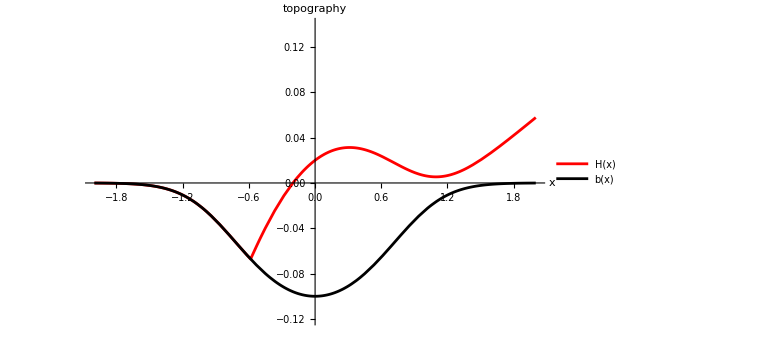

-Graphics-

```mathematica
(*Define H[x]*)
H0 = 0.12;
bmax=0.1;
(*bv = Min[bmax*(x^2-1),0];*)
bv = bmax*(Tanh[x^2]-1);
αv = 0.5;
fv=0.42;

eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*(αv-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*αv)*Exp[ϕ[x]] == fv+D[bv,x] -(αv-D[bv,x])/(1+D[bv,x]*αv);
sollogss = NDSolve[{eqnlogODE,ϕ[0]==Log[H0]},ϕ,{x,-2,2}];
Hnumeric =  Exp[ϕ[x]/.sollogss];
(*Plot results and comparisons*)
Plot[{Hnumeric+bv,bv},{x,-2,2},PlotStyle->{{Red},Black},AxesLabel->{"x","topography"},PlotLegends->{"H(x)","b(x)"},ImageSize->Large,PlotRange->{-1.2*bmax,1.4*bmax},LabelStyle->{FontSize->20}]
```